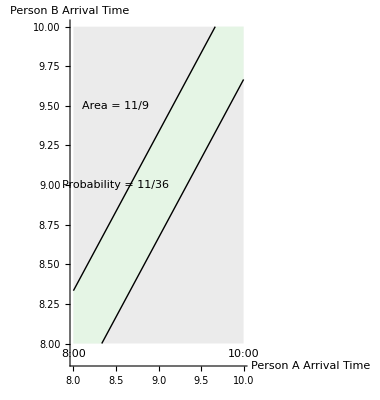

```mathematica
(*问题:
两人约好8到10点在某地见面,谁到了就等对方20分钟再离开,最迟等到10点为止,请问二人相遇的概率
*)
(*时间范围*)tmin=8;
tmax=10;
deltaT=1/3;(*等待时间 20分钟/60分钟=1/3小时*)(*计算面积*)squareArea=(tmax-tmin)^2;
triangleArea=1/2*(2-deltaT)^2;
greenArea=squareArea-2*triangleArea;

(*计算概率*)
probability=Rationalize[greenArea/squareArea];

(*总体时间区域*)
timeArea=Graphics[{Opacity[0.5,LightGray],Rectangle[{tmin,tmin},{tmax,tmax}]},Axes->True];

(*相遇可能的区域*)
meetingArea=Graphics[{Opacity[0.5,LightGreen],Polygon[{{tmin,tmin},{tmin+deltaT,tmin},{tmax,tmax-deltaT},{tmax,tmax},{tmax-deltaT,tmax},{tmin,tmin+deltaT}}]}];

(*标签和线条*)
labels=Graphics[{Line[{{tmin+deltaT,tmin},{tmax,tmax-deltaT}}],Line[{{tmin,tmin+deltaT},{tmax-deltaT,tmax}}],Text["8:00",{tmin,tmin-0.1},{0,-1}],Text["10:00",{tmax,tmin-0.1},{0,-1}],Text[Row[{"Area = ",Rationalize[greenArea]}],{tmin+0.5,tmax-0.5}],Text[Row[{"Probability = ",probability}],{tmin+0.5,tmax-1}]}];

(*显示图形*)
Show[timeArea,meetingArea,labels,Axes->True,AxesLabel->{"Person A Arrival Time","Person B Arrival Time"}]
```